# List #1

## Exercise 2

Loading the PhysicalConstants data set:

```mathematica
<<PhysicalConstants`
?"PhysicalConstants`*"
```

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Speed of light:

```mathematica
SpeedOfLight
```

(299792458 Meter)/Second

Mass of an electron:

```mathematica
ElectronMass
```

9.10938×10^-31 Kilogram

Sun’s radius:

```mathematica
SolarRadius
```

6.9599×10^8 Meter

Mass of a muon:

```mathematica
MuonMass
```

1.88353×10^-28 Kilogram

Planck’s constant:

```mathematica
PlanckConstant
```

6.62607×10^-34 Joule Second

## Exercise 3

Function used to convert units is called UnitConvert and data set of all units is called Quantity.

```mathematica
UnitConvert[Quantity[1,"Pounds"],"Kilograms"]//N
UnitConvert[Quantity[3, "Foots"], "Meters"]//N
UnitConvert[Quantity[1, "Miles"],"Meters"]//N
```

0.453592

0.9144

1609.34

Function converting to SI:

```mathematica
SI[1 Mile]//N
SI[14.5  Atmosphere]//N
SI[1 Ounce]//N
```

1609.34 Meter

```mathematica
1.4692125*^6 Pascal
```

0.0283495 Kilogram

Function converting to CGS:

```mathematica
CGS[5 Kilogram]//N
CGS[100 Meter]//N
CGS[10 Newton]//N
```

5000. Gram

10000. Centimeter

1.×10^6 Dyne

Function converting temperature:

```mathematica
ConvertTemperature[100 ,Celsius,Fahrenheit]
```

212

All components of Quantity:

```mathematica
?Quantity
Quantity[All]
```

RowBox[{"Quantity", "[", RowBox[{StyleBox["magnitude", "TI"], ",", StyleBox["unit", "TI"]}], "]"}] represents a quantity with size StyleBox["magnitude", "TI"] and the unit specified by StyleBox["unit", "TI"].
RowBox[{"Quantity", "[", StyleBox["unit", "TI"], "]"}] assumes the StyleBox["magnitude", "TI"] of the specified StyleBox["unit", "TI"] to be 1.

Quantity::unkunit: Unable to interpret unit specification All.

```mathematica
?Units`*
```

## Exercise 4

Loading CountryData set. Showing list of the european countries and their population:

```mathematica
?CountryData
CountryData["Europe","Name"]
CountryData["Europe","Population"]
Graphics[{Gray,CountryData["Europe","Polygon"],Red,CountryData["Poland","Polygon"],Blue,CountryData["Germany","Polygon"]}]
```

RowBox[{"CountryData", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"tag\",\"TI\"]\)\"", ShowStringCharacters->True], ",", StyleBox["\"\!\(\*StyleBox[\"property\",\"TI\"]\)\"", ShowStringCharacters->True]}], "]"}] gives the value of the specified property for the country, country-like entity, or group of countries specified by "
StyleBox["tag", "TI"]".
RowBox[{"CountryData", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"tag\",\"TI\"]\)\"", ShowStringCharacters->True], ",", RowBox[{"{", RowBox[{StyleBox["property", "TI"], ",", StyleBox["…", "TR"], ",", StyleBox["dates", "TI"]}], "}"}]}], "]"}] gives time series for certain economic and other properties.

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

{3248655,85458,8452081,9469915,10841093,3726569,7300838,4369961,1153409,10611300,5628958,1337821,49709,5434241,64101308,81625599,29111,11470255,65605,9918377,335631,4682042,86159,61175248,95732,1859203,2218123,37313,3264812,536427,2071178,421844,3473640,30508,633506,16806723,5022555,38344752,10705265,21289792,32742,7164132,5497156,2049112,47290504,2637,9595619,7788196,44457736,63556184,839}

-Graphics-

## Exercise 5

Orbits of Earth and Jupiter:

```mathematica
Graphics3D[{Cyan,PlanetData["Earth","OrbitPath"],Magenta,PlanetData["Jupiter","OrbitPath"]}]
```

-Graphics3D-

## Exercise 6

Function used to draw plots in 2 dimensions is Plot

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

Function used to draw plots in three dimensions

```mathematica
?Plot3D
```

Plot3D[f,{x,x_min,x_max},{y,y_min,y_max}] generates a three-dimensional plot of f as a function of x and y. 
Plot3D[{f_1,f_2,…},{x,x_min,x_max},{y,y_min,y_max}] plots several functions.

Plot of functions sin(x) and x^2+1 in limited range

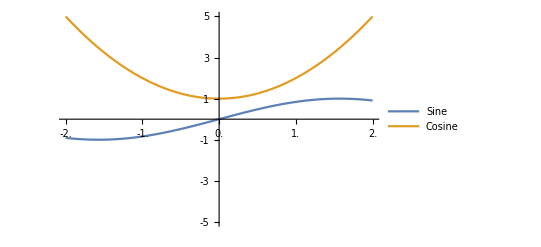

```mathematica
Plot[{Sin[x],x^2+1},{x,-2,2},PlotRange->{{-5,5}},Ticks->{Range[-2,2,0.5],Range[-5,5,1]},PlotLegends->{"Sine","Cosine"}]
```

## Exercise 7

We load VariationalMathods package:

```mathematica
<<VariationalMethods`
?"VariationalMethods`*"
```

```mathematica
e8=EulerEquations[1/2 m r^2 θ'[t]^2+m g r Cos[θ[t]],θ[t],t]
```

-10 Sin[θ[t]]-θ''[t]==0

## Exercise 8

What’s the usage of IntegerQ function:

```mathematica
?IntegerQ
```

IntegerQ[expr] gives True if expr is an integer, and False otherwise.

What’s the usage of EventQ function:

```mathematica
?EvenQ
```

EvenQ[expr] gives True if expr is an even integer, and False otherwise.

What’s the usage of OddQ function:

```mathematica
?OddQ
```

OddQ[expr] gives True if expr is an odd integer, and False otherwise.

What’s the usage of PrimeQ function:

```mathematica
?PrimeQ
```

PrimeQ[expr] yields True if expr is a prime number, and yields False otherwise.

What’s the usage of Positive function:

```mathematica
?Positive
```

Positive[x] gives True if x is a positive number.

What’s the usage of Negative function:

```mathematica
?NonNegative
```

NonNegative[x] gives True if x is a non-negative number.

What’s the usage of NonPositive function:

```mathematica
?NonPositive
```

NonPositive[x] gives True if x is a non-positive number.

What’s the usage of NumberQ function

```mathematica
?NumberQ
```

NumberQ[expr] gives True if expr is a number, and False otherwise.

What’s the usage of NumericQ function

```mathematica
?NumericQ
```

NumericQ[expr] gives True if expr is a numeric quantity, and False otherwise.

## Exercise 9

We define function which returns i-th digit of Pi after coma.

```mathematica
F[i_]:=RealDigits[N[Pi,i+1]][[1]][[i+1]]
F[0]
F[1]
F[2]
F[106]
F[10106]
```

3

1

4

1

8

## Exercise 10

We define function which returns i-th digit of  Euler constant after coma.

```mathematica
W[i_]:=RealDigits[N[E,i+1]][[1]][[i+1]]
W[0]
W[1]
W[2]
W[100]
```

2

7

2

4

## Exercise 11

We plot some graphs of the special functions.

```mathematica
Plot[Hypergeometric2F1
```

## Exercise 12

## Exercise 13

## Exercise 14

Let’s find the solution of differential euqation we got in exercise 7.

{{θ[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}}

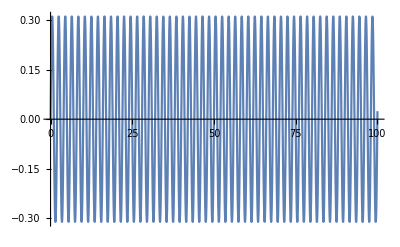

```mathematica
m=1;
r=1;
g=10;
sol=NDSolve[{e8,θ[0]== 0, θ'[0]== 1},θ[t],{t,0,100}]
Plot[Sin[θ[t]/.sol]*r,{t,0,100}]
```

## Exercise 15

We animate movement of a membrane.